```mathematica
a[k_]:= (((-1)^k (4k+3)(2k)!)/(2^(2k+1) k! (k+1)!));
```

```mathematica
S[x_,N_]=10 Sum[a[n] LegendreP[2n+1,x],{n,0,N}];
```

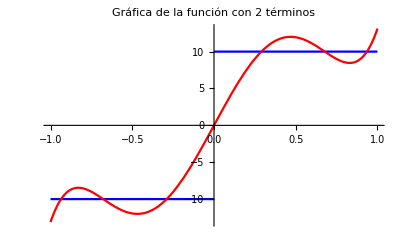

```mathematica
Plot[{Piecewise[{{-10, x <0},{10, x <1}}],S[x,2]},{x,-1,1}, PlotLabel->Style["Gráfica de la función con 2 términos", FontSize->16], PlotStyle->{Blue, Red}]
```

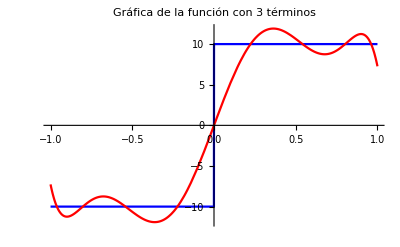

```mathematica
Plot[{Piecewise[{{-10, x <0},{10, x <1}}],S[x,3]},{x,-1,1}, PlotLabel->Style["Gráfica de la función con 3 términos", FontSize->16], PlotStyle->{Blue, Red}]
```

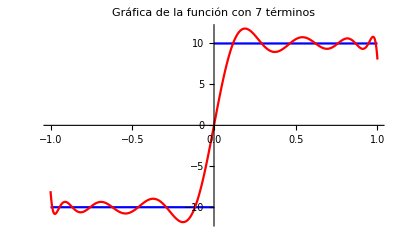

```mathematica
Plot[{Piecewise[{{-10, x <0},{10, x <1}}],S[x,7]},{x,-1,1}, PlotLabel->Style["Gráfica de la función con 7 términos", FontSize->16], PlotStyle->{Blue, Red}]
```

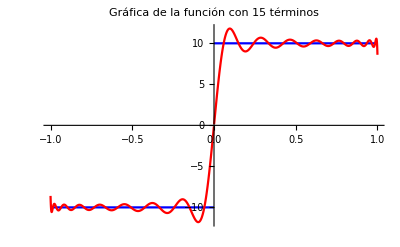

```mathematica
Plot[{Piecewise[{{-10, x <0},{10, x <1}}],S[x,15]},{x,-1,1}, PlotLabel->Style["Gráfica de la función con 15 términos", FontSize->16], PlotStyle->{Blue, Red}]
```

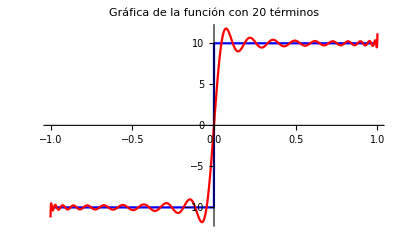

```mathematica
Plot[{Piecewise[{{-10, x <0},{10, x <1}}],S[x,20]},{x,-1,1}, PlotLabel->Style["Gráfica de la función con 20 términos", FontSize->16], PlotStyle->{Blue, Red}]
```

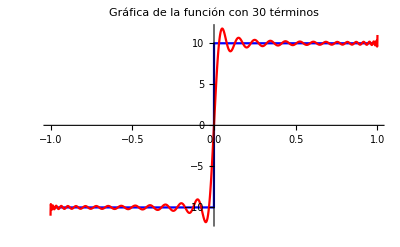

```mathematica
Plot[{Piecewise[{{-10, x <0},{10, x <1}}],S[x,30]},{x,-1,1}, PlotLabel->Style["Gráfica de la función con 30 términos", FontSize->16], PlotStyle->{Blue, Red}]
```